```mathematica
data=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/time_domain_results.txt","Table"];
Dimensions[data]
```

{2048,3}

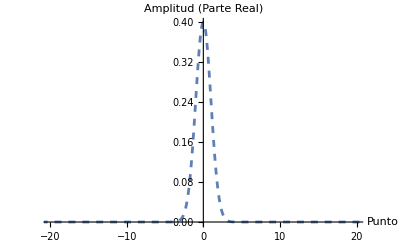

```mathematica
(*Graficar la parte real de los resultados*)realPlot=ListPlot[Transpose[{data[[All,1]],data[[All,2]]}],PlotStyle->Dashed,AxesLabel->{"Punto","Amplitud (Parte Real)"},Joined->True,PlotRange->{{-20,20},All}]
```

```mathematica
InverseFourierTransform[Exp[-ω^2/(2*σ^2)],ω,t,FourierParameters->{1, 1}]//FullSimplify
```

(ⅇ^(-1/2 t^2 σ^2))/(√(2 π) √(1/σ^2))

```mathematica
Funcion[t_,σ_]:=σ √(1/(2π))*Exp[(-t^2*σ^2)/2];
```

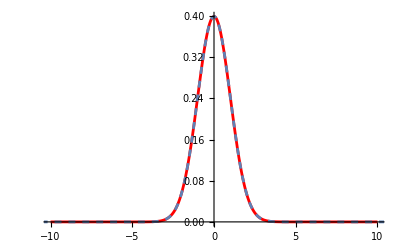

```mathematica
Show[Plot[Funcion[t,1],{t,-10,10},PlotStyle->Red,PlotRange->{{-10,10},All}],realPlot,PlotRange->{{-10,10},All}]
```